```mathematica
ca=Table[Import["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[x]<>"_0.5.dat"],{x,Range[10,80,10]}]
```

{{{0.,3.02453×10^-8},{0.01,3.0138×10^-8},{0.02,3.00008×10^-8},{0.03,2.98033×10^-8},{0.04,2.97067×10^-8},{0.05,2.96623×10^-8},{0.06,2.95139×10^-8},{0.07,2.94394×10^-8},{0.08,2.93659×10^-8},{0.09,2.93745×10^-8},{0.1,2.9282×10^-8},{0.11,2.92421×10^-8},{0.12,2.92413×10^-8},325,{3.38,5.00986×10^-8},{3.39,4.60884×10^-8},{3.4,4.25955×10^-8},{3.41,3.93181×10^-8},{3.42,3.64413×10^-8},{3.43,3.37553×10^-8},{3.44,3.15888×10^-8},{3.45,2.93958×10^-8},{3.46,2.78011×10^-8},{3.47,2.61125×10^-8},{3.48,2.46797×10^-8},{3.49,2.32747×10^-8},{3.5,2.19345×10^-8}},6,{1}}
 |  |  |  |

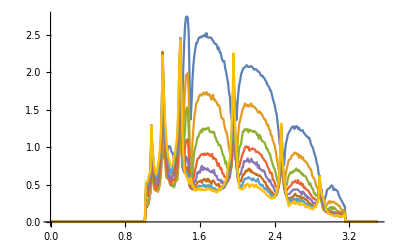

```mathematica
ListLinePlot[ca]
```

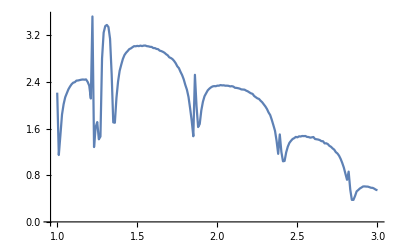
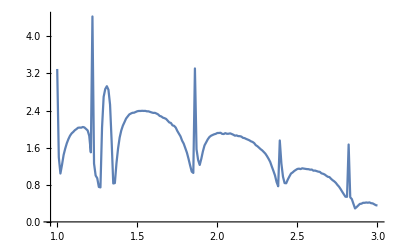
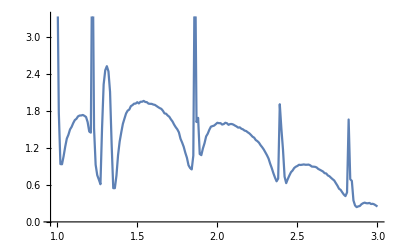
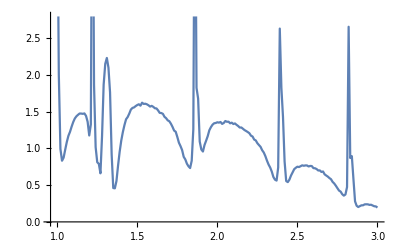
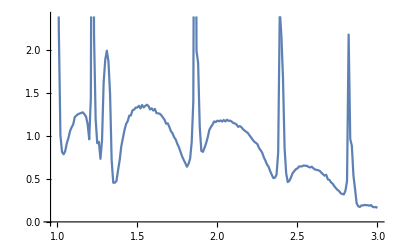
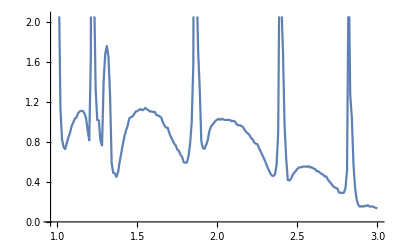
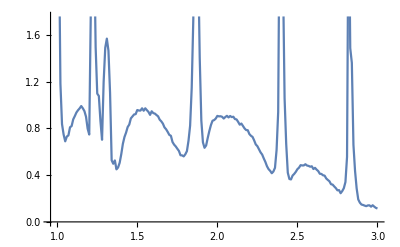
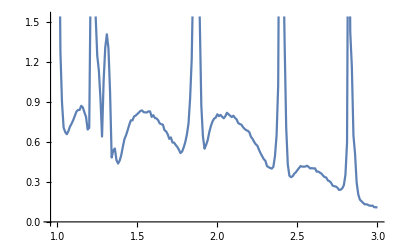
{{10,-Graphics-},{20,-Graphics-},{30,-Graphics-},{40,-Graphics-},{50,-Graphics-},{60,-Graphics-},{70,-Graphics-},{80,-Graphics-}}

```mathematica
Table[{5x,ListLinePlot[ca[[x]]]},{x,Range[2,16,2]}]
```

```mathematica
trainingset[ω_]:=Table[10*n->ca[[n]][[ω*100+1,2]],{n,Range[1,8,1]}]
```

```mathematica
trainingset[0.01]
```

{10→1.14849,20→1.39334,30→1.77799,40→2.00867,50→2.24142,60→2.44256,70→2.57183,80→2.7817}

```mathematica
data[x_,ω_]:=data[x,ω]=Module[{P},P=Predict[trainingset[ω],Method->"NeuralNetwork"];(*{P[x]+StandardDeviation[P[x,"Distribution"]],P[x]-StandardDeviation[P[x,"Distribution"]],*)P[x]]
```

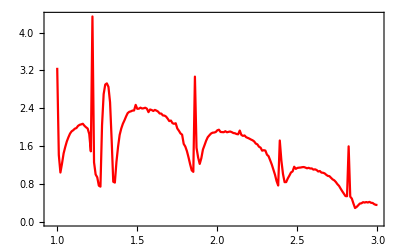

```mathematica
ListLinePlot[Table[{x+1,data[20,x]},{x,Range[0,2,0.01]}],Frame->True,PlotStyle->Red]
```

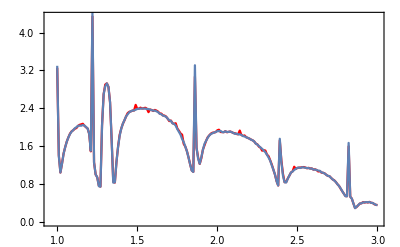

```mathematica
Show[%40,ListLinePlot[ca[[2]]]]
```

```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,5000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Inverse[β[ω,δ,t,ϵ1,ϵ2,m]]
SR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ1,ϵ2,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ1,ϵ2,m].T1[t,m]].g[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].SR[ω,δ,t,ϵ2,ϵ1,m].ConjugateTranspose[ρ[t,m]]].SL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]].SR[ω,δ,t,ϵ2,ϵ1,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IL[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IL[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IR[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IR[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].IL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].grr[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m]]]
```

```mathematica
tr[2,0.001,1,-0.75,1,9]//AbsoluteTiming
```

{0.002592,3.00019}

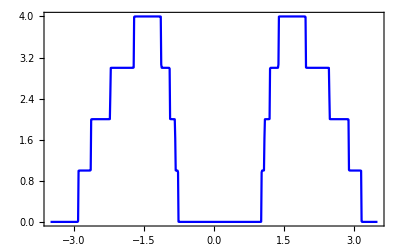

```mathematica
ListLinePlot[ParallelTable[{ω,Print["working on "<>ToString[ω]<>""];tr[ω,0.001,1,-0.75,1,9]},{ω,Range[-3.5,3.5,0.01]}],Frame->True,PlotStyle->Blue]
```

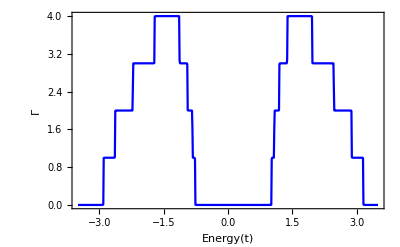

```mathematica
Show[%19,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy[t]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```